-5.00391+0.000530695 x

-0.519656+0.0001691 x+2.22402×10^-9 x^2

-1.67871+0.000378947 x-9.51029×10^-10 x^2+1.11022×10^-14 x^3

-0.141273-0.0000406877 x+1.08914×10^-8 x^2-9.16426×10^-14 x^3+2.70052×10^-19 x^4

0.516742-0.000566326 x+9.99756×10^-8 x^2-5.90874×10^-12 x^3+1.70318×10^-16 x^4-2.50739×10^-21 x^5+1.94326×10^-26 x^6-7.5416×10^-32 x^7+1.15235×10^-37 x^8

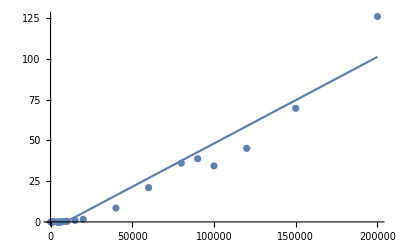

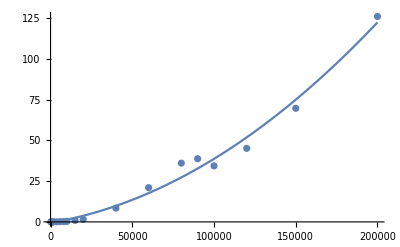

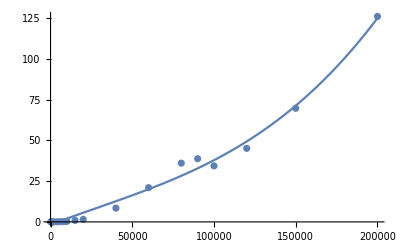

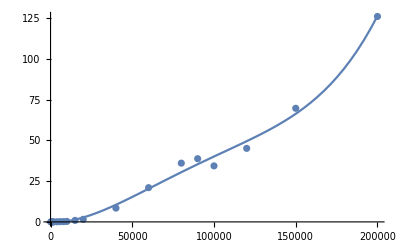

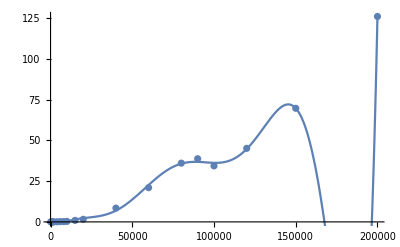

```mathematica
burbujaSimple1=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x},x]

burbujaSimple2=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2},x]

burbujaSimple3=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2,x^3},x]

burbujaSimple4=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2,x^3,x^4},x]

burbujaSimple8=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}}]

g1=Plot[burbujaSimple1,{x,0,200000}]
Show[puntos,g1]

g2=Plot[burbujaSimple2,{x,0,200000}]
Show[puntos,g2]

g3=Plot[burbujaSimple3,{x,0,200000}]
Show[puntos,g3]

g4=Plot[burbujaSimple4,{x,0,200000}]
Show[puntos,g4]

g8=Plot[burbujaSimple8,{x,0,200000}]
Show[puntos,g8]
```